```mathematica
Plot[-Log[x/10]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot[-Log[x/20]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot[-Log[10000/x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot3D[-Log[y/x],{x,2,2.5},{y,20000,25000}]
```

-Graphics3D-

```mathematica
def round_figures(x,n):
round(x,int(n-math.ceil(math.log10(abs(x)))))

T=round_figures(T/1.5,2)

Plot[2-Ceiling(Log10(Abs(x))),{x,500,1500}]
```

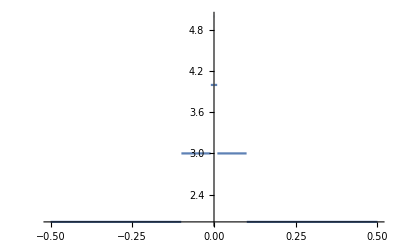

```mathematica
Plot[2-Ceiling[Log10[Abs[x]]],{x,-0.5,0.5}]
```

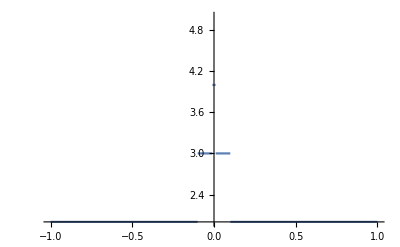

```mathematica
Plot[2-Ceiling[Log10[Abs[x]]],{x,-1,1},PlotPoints->91,MaxRecursion->6]
```

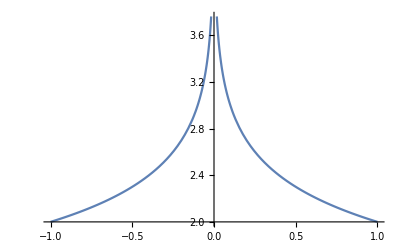

```mathematica
Plot[2-Log10[Abs[x]],{x,-1,1},PlotPoints->91,MaxRecursion->6]
```

```mathematica
Tfactor=-math.log(self.Tmax/self.Tmin)
T=self.Tmax*math.exp(Tfactor*step/self.steps)
```

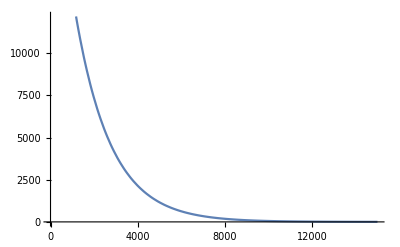

```mathematica
Plot[25000*Exp[-Log[25000/2.5]*step/15000],{step,1,15000}]
```

```mathematica
math.exp(-dE/T)
```

```mathematica
Plot3D[Exp[-x/(25000*Exp[-Log[25000/2.5]*step/15000])],{step,1,15000}]
```

Plot3D[Exp[-x/(25000 Exp[-(Log[25000/2.5] step)/15000])],{step,1,15000}]

```mathematica
Plot3D[Exp[-x/(25000*Exp[-Log[25000/2.5]*step/15000])],{x,1,1000},{step,1,15000}]
```

-Graphics3D-